Practical 3

Plotting of third order solution family of differential equations 
Ques. 1 Solve third order differential equations (d^3 y)/dx^3-5 (d^2 y)/dx^2+ 8 dy/dx-4y = 0  and plot it’s any three solutions.

```mathematica
sol = DSolve[y'''[x] - 5y''[x]+8y'[x]- 4y[x] == 0, y[x], x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(2 x) x C[3]}}

```mathematica
sol1 = Evaluate[y[x]/.sol[[1]]/.{C[1]-> 1, C[2]-> 2, C[3]-> 2/3}]
```

ⅇ^x+2 ⅇ^(2 x)+2/3 ⅇ^(2 x) x

```mathematica
sol2 = Evaluate[y[x]/.sol[[1]]/.{C[1]->0.5, C[2]->2, C[3]->3}]
```

0.5 ⅇ^x+2 ⅇ^(2 x)+3 ⅇ^(2 x) x

```mathematica
sol3 = Evaluate[y[x]/.sol[[1]]/.{C[1]->-1, C2[2]->-2, C[3]-> 0.5}]
```

-ⅇ^x+0.5 ⅇ^(2 x) x+ⅇ^(2 x) C[2]

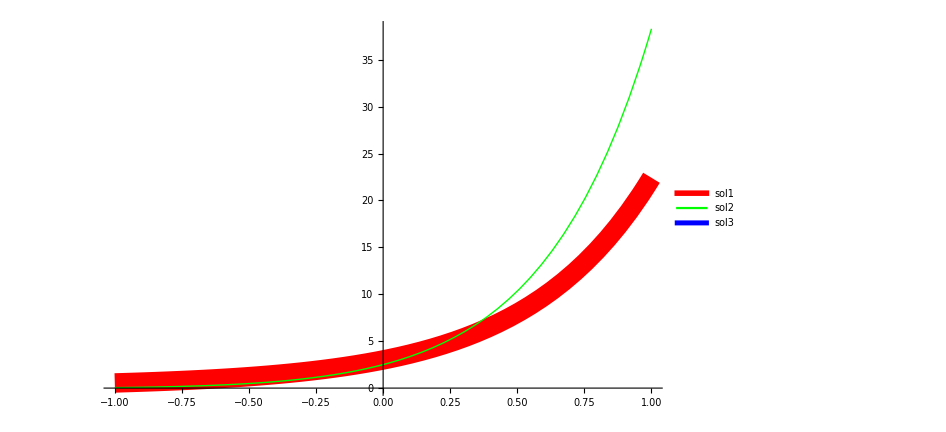

```mathematica
Plot[{sol1, sol2, sol3}, {x, - 1, 1}, ImageSize-> 700, PlotStyle->{{Red, Thickness[0.02]}, {Green, Thick}, {Blue, Thickness[0.01]}}, PlotLegends->Placed[LineLegend["Expressions", LegendLayout-> "Column", LegendFunction->"Frame"], {0.15, 0.87}]]
```

```mathematica
SOL=DSolve[y'''[x]+3y''[x]-25y'[x]+21y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-7 x) C[1]+ⅇ^x C[2]+ⅇ^(3 x) C[3]}}

```mathematica
sol1=Evaluate[y[x]/.SOL[[1]]/.{C[1]->2,C[2]->2,C[3]->2/3}]
```

2 ⅇ^(-7 x)+2 ⅇ^x+(2 ⅇ^(3 x))/3

```mathematica
sol2=Evaluate[y[x]/.SOL[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

ⅇ^(-7 x)+2 ⅇ^x+3 ⅇ^(3 x)

```mathematica
sol3=Evaluate[y[x]/.SOL[[1]]/.{C[1]->0,C[2]->2,C[3]->2}]
```

2 ⅇ^x+2 ⅇ^(3 x)

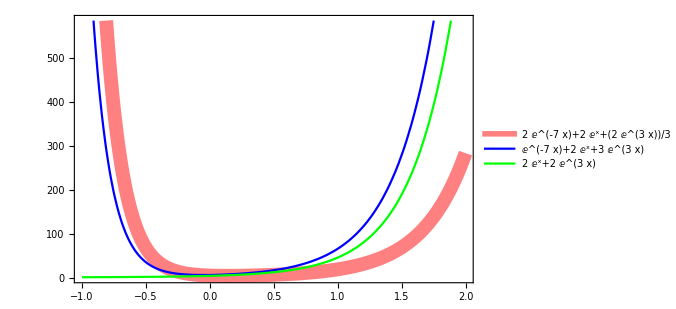

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,2},PlotStyle-> {{Pink,Thickness[0.02]},Blue,Green},Frame->True,ImageSize->500,PlotLegends->{sol1,sol2,sol3}]
```

```mathematica
pol=DSolve[y'''[x]-4y''[x]-25y'[x]+28y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^x C[2]+ⅇ^(7 x) C[3]}}

```mathematica
pol1=Evaluate[y[x]/.pol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

ⅇ^(-4 x)+2 ⅇ^x+3 ⅇ^(7 x)

```mathematica
pol2=Evaluate[y[x]/.pol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->1.3}]
```

-ⅇ^(-4 x)-2 ⅇ^x+1.3 ⅇ^(7 x)

```mathematica
pol3=Evaluate[y[x]/.pol[[1]]/.{C[1]->3/2,C[2]->0.5,C[3]->-2.5}]
```

(3 ⅇ^(-4 x))/2+0.5 ⅇ^x-2.5 ⅇ^(7 x)

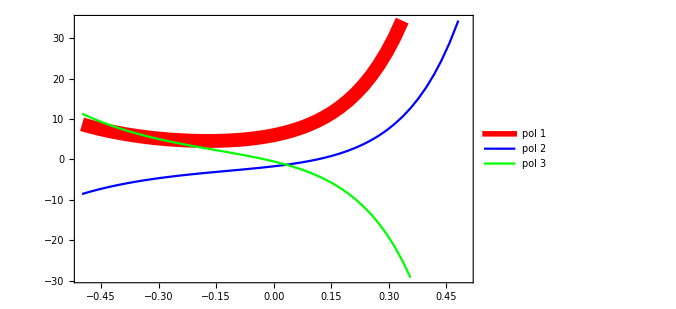

```mathematica
Plot[{pol1,pol2,pol3},{x,-0.5,0.5},PlotStyle-> {{Red,Thickness[0.02]},Blue,Green},Frame->True,ImageSize->500,PlotLegends->LineLegend[{"pol 1","pol 2","pol 3"}]]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(11 x) C[3]+(17 Cos[2 x]+6 Sin[2 x])/1625}}

ⅇ^-x+2 ⅇ^(3 x)+(2 ⅇ^(11 x))/3+(17 Cos[2 x]+6 Sin[2 x])/1625

-ⅇ^-x+2 ⅇ^(3 x)+1.3 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

(3 ⅇ^-x)/2+0.2 ⅇ^(3 x)-2.3 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

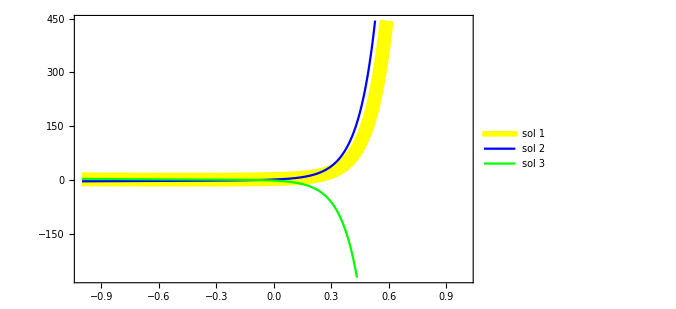

```mathematica
SOL=DSolve[y'''[x]-13y''[x]+19y'[x]+33y[x]==Cos[2x],y[x],x]
sol1=Evaluate[y[x]/.SOL[[1]]/.{C[1]->1,C[2]->2,C[3]->2/3}]
sol2=Evaluate[y[x]/.SOL[[1]]/.{C[1]->-1,C[2]->2,C[3]->1.3}]
sol3=Evaluate[y[x]/.SOL[[1]]/.{C[1]->3/2,C[2]->0.2,C[3]->-2.3}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle-> {{Yellow,Thickness[0.02]},Blue,Green},Frame->True,ImageSize->500,PlotLegends->Placed[{"sol 1","sol 2","sol 3"},Below]]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(4 x) C[3]}}

ⅇ^-x+2 ⅇ^(3 x)+(2 ⅇ^(4 x))/3

-ⅇ^-x+2 ⅇ^(3 x)+1.3 ⅇ^(4 x)

(3 ⅇ^-x)/2+0.2 ⅇ^(3 x)-2.3 ⅇ^(4 x)

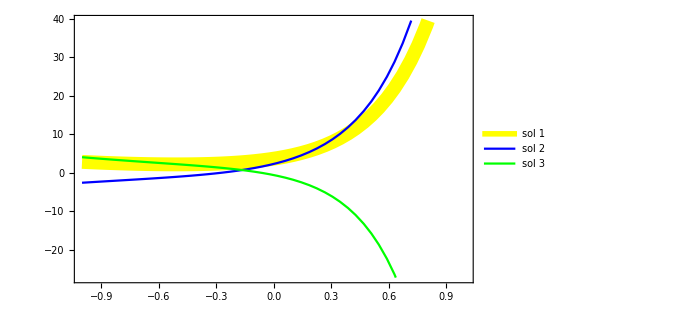

```mathematica
SOL=DSolve[y'''[x]-6y''[x]+5y'[x]+12y[x]==0,y[x],x]
sol1=Evaluate[y[x]/.SOL[[1]]/.{C[1]->1,C[2]->2,C[3]->2/3}]
sol2=Evaluate[y[x]/.SOL[[1]]/.{C[1]->-1,C[2]->2,C[3]->1.3}]
sol3=Evaluate[y[x]/.SOL[[1]]/.{C[1]->3/2,C[2]->0.2,C[3]->-2.3}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle-> {{Yellow,Thickness[0.02]},Blue,Green},Frame->True,ImageSize->500,PlotLegends->Placed[{"sol 1","sol 2","sol 3"},Below]]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(3 x) C[3]}}

ⅇ^x+2 ⅇ^(2 x)+(2 ⅇ^(3 x))/3

-ⅇ^x+2 ⅇ^(2 x)+1.3 ⅇ^(3 x)

(3 ⅇ^x)/2+0.2 ⅇ^(2 x)-2.3 ⅇ^(3 x)

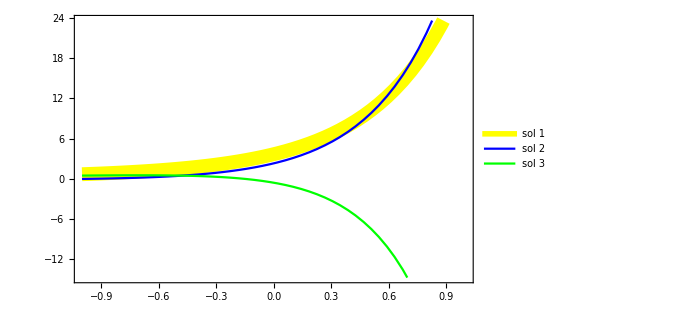

```mathematica
SOL=DSolve[y'''[x]-6y''[x]+11y'[x]-6y[x]==0,y[x],x]
sol1=Evaluate[y[x]/.SOL[[1]]/.{C[1]->1,C[2]->2,C[3]->2/3}]
sol2=Evaluate[y[x]/.SOL[[1]]/.{C[1]->-1,C[2]->2,C[3]->1.3}]
sol3=Evaluate[y[x]/.SOL[[1]]/.{C[1]->3/2,C[2]->0.2,C[3]->-2.3}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle-> {{Yellow,Thickness[0.02]},Blue,Green},Frame->True,ImageSize->500,PlotLegends->Placed[{"sol 1","sol 2","sol 3"},Left]]
```

{{y[x]→C[3]-x Cos[x]-C[2] Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+C[1] Sin[x]+Log[Cos[x]] Sin[x]}}

2/3-2 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+Sin[x]+Log[Cos[x]] Sin[x]

1.3-2 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]-Sin[x]+Log[Cos[x]] Sin[x]

-2.3-0.2 Cos[x]-x Cos[x]-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+(3 Sin[x])/2+Log[Cos[x]] Sin[x]

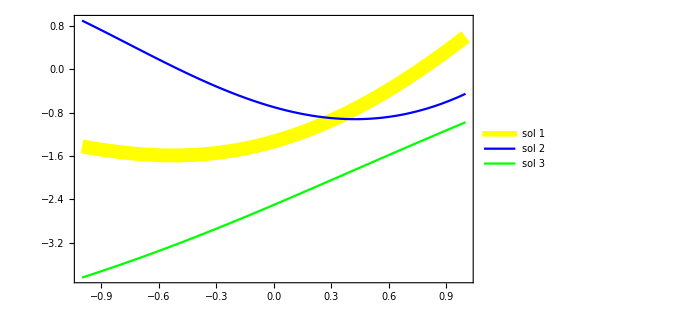

```mathematica
SOL=DSolve[y'''[x]+y'[x]==Sec[x],y[x],x]
sol1=Evaluate[y[x]/.SOL[[1]]/.{C[1]->1,C[2]->2,C[3]->2/3}]
sol2=Evaluate[y[x]/.SOL[[1]]/.{C[1]->-1,C[2]->2,C[3]->1.3}]
sol3=Evaluate[y[x]/.SOL[[1]]/.{C[1]->3/2,C[2]->0.2,C[3]->-2.3}]
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle-> {{Yellow,Thickness[0.02]},Blue,Green},Frame->True,ImageSize->500,PlotLegends->Placed[{"sol 1","sol 2","sol 3"},Right]]
```